```mathematica
Charsimp[x_,f_,theta_]=1/(12 f (-4+3 f^2))(2 f x (52-22 √(4-3 f^2)-24 x^2+3 f^2 (-13+6 x^2))+3 (-8 (-2+√(4-3 f^2)) (-5+2 x^2)+f^2 (60-17 √(4-3 f^2)+4 (-6+5 √(4-3 f^2)) x^2)) Cos[theta]-18 f (-4+3 f^2+2 √(4-3 f^2)) x Cos[2 theta]+3 (-3 f^2 (-4+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[3 theta])
```

1/(12 f (-4+3 f^2))(2 f x (52-22 √(4-3 f^2)-24 x^2+3 f^2 (-13+6 x^2))+3 (-8 (-2+√(4-3 f^2)) (-5+2 x^2)+f^2 (60-17 √(4-3 f^2)+4 (-6+5 √(4-3 f^2)) x^2)) Cos[theta]-18 f (-4+3 f^2+2 √(4-3 f^2)) x Cos[2 theta]+3 (-3 f^2 (-4+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[3 theta])

```mathematica
kai[f_,theta_]=Simplify[Solve[Charsimp[x,f,theta]==0,x,{Element[x,Reals],Element[f,Reals],Element[theta,Reals],}]]
```

{{x→1/(3 f (-4+3 f^2))(-(8-4 √(4-3 f^2)+f^2 (-6+5 √(4-3 f^2))) Cos[theta]+((-4+3 f^2) (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta]))/(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3)+(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3))},{x→1/(6 f (-4+3 f^2))(-2 (8-4 √(4-3 f^2)+f^2 (-6+5 √(4-3 f^2))) Cos[theta]-(ⅈ (-ⅈ+√3) (-4+3 f^2) (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta]))/(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3)+ⅈ (ⅈ+√3) (-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3))},{x→1/(6 f (-4+3 f^2))(-2 (8-4 √(4-3 f^2)+f^2 (-6+5 √(4-3 f^2))) Cos[theta]+(ⅈ (ⅈ+√3) (-4+3 f^2) (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta]))/(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3)-ⅈ (-ⅈ+√3) (-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3))}}

```mathematica
Plot3D[kai[f,theta],{f,0,1},{theta,0,Pi}]
```

Power::infy: 無限式1/0.が見付かりました．

Power::infy: 無限式1/0.^1/3が見付かりました．

∞::indet: 不定式0.\ ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

General::stop: 計算中，Power :: "infy"のこれ以上の出力は表示されません．

∞::indet: 不定式0.\ ⅈ\ (-ⅈ + √3)\ ComplexInfinityが見付かりました．

∞::indet: 不定式0.\ ⅈ\ (ⅈ + √3)\ ComplexInfinityが見付かりました．

General::stop: 計算中，∞ :: "indet"のこれ以上の出力は表示されません．

-Graphics3D-

```mathematica
kai1[f_,tehta_]=-(8 Cos[theta]-6 f^2 Cos[theta]-4 √(4-3 f^2) Cos[theta]+5 f^2 √(4-3 f^2) Cos[theta])/(3 (-4 f+3 f^3))-(-144 (8 Cos[theta]-6 f^2 Cos[theta]-4 √(4-3 f^2) Cos[theta]+5 f^2 √(4-3 f^2) Cos[theta])^2-72 (-4 f+3 f^3) (-52 f+39 f^3+22 f √(4-3 f^2)-36 f Cos[2 theta]+27 f^3 Cos[2 theta]+18 f √(4-3 f^2) Cos[2 theta]))/(18 2^(2/3) (-4 f+3 f^3) ((6967296 f^2 Cos[theta]-13851648 f^4 Cos[theta]+9020160 f^6 Cos[theta]-1912896 f^8 Cos[theta]-3483648 f^2 √(4-3 f^2) Cos[theta]+5702400 f^4 √(4-3 f^2) Cos[theta]-2674944 f^6 √(4-3 f^2) Cos[theta]+268272 f^8 √(4-3 f^2) Cos[theta]-7077888 Cos[theta]^3+25214976 f^2 Cos[theta]^3-34172928 f^4 Cos[theta]^3+20653056 f^6 Cos[theta]^3-4665600 f^8 Cos[theta]^3+3538944 √(4-3 f^2) Cos[theta]^3-11280384 f^2 √(4-3 f^2) Cos[theta]^3+13105152 f^4 √(4-3 f^2) Cos[theta]^3-6704640 f^6 √(4-3 f^2) Cos[theta]^3+1296000 f^8 √(4-3 f^2) Cos[theta]^3-5971968 f^2 Cos[theta] Cos[2 theta]+14929920 f^4 Cos[theta] Cos[2 theta]-12317184 f^6 Cos[theta] Cos[2 theta]+3359232 f^8 Cos[theta] Cos[2 theta]+2985984 f^2 √(4-3 f^2) Cos[theta] Cos[2 theta]-6345216 f^4 √(4-3 f^2) Cos[theta] Cos[2 theta]+4478976 f^6 √(4-3 f^2) Cos[theta] Cos[2 theta]-1049760 f^8 √(4-3 f^2) Cos[theta] Cos[2 theta]+2985984 f^2 Cos[3 theta]-6718464 f^4 Cos[3 theta]+5038848 f^6 Cos[3 theta]-1259712 f^8 Cos[3 theta]-1492992 f^2 √(4-3 f^2) Cos[3 theta]+2799360 f^4 √(4-3 f^2) Cos[3 theta]-1679616 f^6 √(4-3 f^2) Cos[3 theta]+314928 f^8 √(4-3 f^2) Cos[3 theta]+√(4 (-144 (8 Cos[theta]-6 f^2 Cos[theta]-4 √(4-3 f^2) Cos[theta]+5 f^2 √(4-3 f^2) Cos[theta])^2-72 (-4 f+3 f^3) (-52 f+39 f^3+22 f √(4-3 f^2)-36 f Cos[2 theta]+27 f^3 Cos[2 theta]+18 f √(4-3 f^2) Cos[2 theta]))^3+(6967296 f^2 Cos[theta]-13851648 f^4 Cos[theta]+9020160 f^6 Cos[theta]-1912896 f^8 Cos[theta]-3483648 f^2 √(4-3 f^2) Cos[theta]+5702400 f^4 √(4-3 f^2) Cos[theta]-2674944 f^6 √(4-3 f^2) Cos[theta]+268272 f^8 √(4-3 f^2) Cos[theta]-7077888 Cos[theta]^3+25214976 f^2 Cos[theta]^3-34172928 f^4 Cos[theta]^3+20653056 f^6 Cos[theta]^3-4665600 f^8 Cos[theta]^3+3538944 √(4-3 f^2) Cos[theta]^3-11280384 f^2 √(4-3 f^2) Cos[theta]^3+13105152 f^4 √(4-3 f^2) Cos[theta]^3-6704640 f^6 √(4-3 f^2) Cos[theta]^3+1296000 f^8 √(4-3 f^2) Cos[theta]^3-5971968 f^2 Cos[theta] Cos[2 theta]+14929920 f^4 Cos[theta] Cos[2 theta]-12317184 f^6 Cos[theta] Cos[2 theta]+3359232 f^8 Cos[theta] Cos[2 theta]+2985984 f^2 √(4-3 f^2) Cos[theta] Cos[2 theta]-6345216 f^4 √(4-3 f^2) Cos[theta] Cos[2 theta]+4478976 f^6 √(4-3 f^2) Cos[theta] Cos[2 theta]-1049760 f^8 √(4-3 f^2) Cos[theta] Cos[2 theta]+2985984 f^2 Cos[3 theta]-6718464 f^4 Cos[3 theta]+5038848 f^6 Cos[3 theta]-1259712 f^8 Cos[3 theta]-1492992 f^2 √(4-3 f^2) Cos[3 theta]+2799360 f^4 √(4-3 f^2) Cos[3 theta]-1679616 f^6 √(4-3 f^2) Cos[3 theta]+314928 f^8 √(4-3 f^2) Cos[3 theta])^2)))^(1/3))+1/(36 2^(1/3) (-4 f+3 f^3))((6967296 f^2 Cos[theta]-13851648 f^4 Cos[theta]+9020160 f^6 Cos[theta]-1912896 f^8 Cos[theta]-3483648 f^2 √(4-3 f^2) Cos[theta]+5702400 f^4 √(4-3 f^2) Cos[theta]-2674944 f^6 √(4-3 f^2) Cos[theta]+268272 f^8 √(4-3 f^2) Cos[theta]-7077888 Cos[theta]^3+25214976 f^2 Cos[theta]^3-34172928 f^4 Cos[theta]^3+20653056 f^6 Cos[theta]^3-4665600 f^8 Cos[theta]^3+3538944 √(4-3 f^2) Cos[theta]^3-11280384 f^2 √(4-3 f^2) Cos[theta]^3+13105152 f^4 √(4-3 f^2) Cos[theta]^3-6704640 f^6 √(4-3 f^2) Cos[theta]^3+1296000 f^8 √(4-3 f^2) Cos[theta]^3-5971968 f^2 Cos[theta] Cos[2 theta]+14929920 f^4 Cos[theta] Cos[2 theta]-12317184 f^6 Cos[theta] Cos[2 theta]+3359232 f^8 Cos[theta] Cos[2 theta]+2985984 f^2 √(4-3 f^2) Cos[theta] Cos[2 theta]-6345216 f^4 √(4-3 f^2) Cos[theta] Cos[2 theta]+4478976 f^6 √(4-3 f^2) Cos[theta] Cos[2 theta]-1049760 f^8 √(4-3 f^2) Cos[theta] Cos[2 theta]+2985984 f^2 Cos[3 theta]-6718464 f^4 Cos[3 theta]+5038848 f^6 Cos[3 theta]-1259712 f^8 Cos[3 theta]-1492992 f^2 √(4-3 f^2) Cos[3 theta]+2799360 f^4 √(4-3 f^2) Cos[3 theta]-1679616 f^6 √(4-3 f^2) Cos[3 theta]+314928 f^8 √(4-3 f^2) Cos[3 theta]+√(4 (-144 (8 Cos[theta]-6 f^2 Cos[theta]-4 √(4-3 f^2) Cos[theta]+5 f^2 √(4-3 f^2) Cos[theta])^2-72 (-4 f+3 f^3) (-52 f+39 f^3+22 f √(4-3 f^2)-36 f Cos[2 theta]+27 f^3 Cos[2 theta]+18 f √(4-3 f^2) Cos[2 theta]))^3+(6967296 f^2 Cos[theta]-13851648 f^4 Cos[theta]+9020160 f^6 Cos[theta]-1912896 f^8 Cos[theta]-3483648 f^2 √(4-3 f^2) Cos[theta]+5702400 f^4 √(4-3 f^2) Cos[theta]-2674944 f^6 √(4-3 f^2) Cos[theta]+268272 f^8 √(4-3 f^2) Cos[theta]-7077888 Cos[theta]^3+25214976 f^2 Cos[theta]^3-34172928 f^4 Cos[theta]^3+20653056 f^6 Cos[theta]^3-4665600 f^8 Cos[theta]^3+3538944 √(4-3 f^2) Cos[theta]^3-11280384 f^2 √(4-3 f^2) Cos[theta]^3+13105152 f^4 √(4-3 f^2) Cos[theta]^3-6704640 f^6 √(4-3 f^2) Cos[theta]^3+1296000 f^8 √(4-3 f^2) Cos[theta]^3-5971968 f^2 Cos[theta] Cos[2 theta]+14929920 f^4 Cos[theta] Cos[2 theta]-12317184 f^6 Cos[theta] Cos[2 theta]+3359232 f^8 Cos[theta] Cos[2 theta]+2985984 f^2 √(4-3 f^2) Cos[theta] Cos[2 theta]-6345216 f^4 √(4-3 f^2) Cos[theta] Cos[2 theta]+4478976 f^6 √(4-3 f^2) Cos[theta] Cos[2 theta]-1049760 f^8 √(4-3 f^2) Cos[theta] Cos[2 theta]+2985984 f^2 Cos[3 theta]-6718464 f^4 Cos[3 theta]+5038848 f^6 Cos[3 theta]-1259712 f^8 Cos[3 theta]-1492992 f^2 √(4-3 f^2) Cos[3 theta]+2799360 f^4 √(4-3 f^2) Cos[3 theta]-1679616 f^6 √(4-3 f^2) Cos[3 theta]+314928 f^8 √(4-3 f^2) Cos[3 theta])^2)))^(1/3)
```

```mathematica
Simplify[kai1[f,theta]]
```

```mathematica
kai1sim[f_,theta_]=1/(3 f (-4+3 f^2))(-(8-4 √(4-3 f^2)+f^2 (-6+5 √(4-3 f^2))) Cos[theta]+((-4+3 f^2) (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta]))/(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3)+(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3))
```

```mathematica
Plot3D[kai1sim[f,theta],{f,0,1},{theta,0,Pi}]
```

-Graphics3D-

```mathematica
kai2sim[f_,theta]=1/(6 f (-4+3 f^2))(-2 (8-4 √(4-3 f^2)+f^2 (-6+5 √(4-3 f^2))) Cos[theta]-(ⅈ (-ⅈ+√3) (-4+3 f^2) (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta]))/(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3)+ⅈ (ⅈ+√3) (-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3))
```

```mathematica
FullSimplify[kai2sim[f,theta]]
```

```mathematica
Plot3D[kai2sim[f,theta],{f,0,1},{theta,0,Pi}]
```

-Graphics3D-

```mathematica
kai3sim[f_,theta_]=1/(6 f (-4+3 f^2))(-2 (8-4 √(4-3 f^2)+f^2 (-6+5 √(4-3 f^2))) Cos[theta]+(ⅈ (ⅈ+√3) (-4+3 f^2) (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta]))/(-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3)-ⅈ (-ⅈ+√3) (-1536 Cos[theta]+6624 f^2 Cos[theta]-9264 f^4 Cos[theta]+5310 f^6 Cos[theta]-1080 f^8 Cos[theta]+768 √(4-3 f^2) Cos[theta]-3024 f^2 √(4-3 f^2) Cos[theta]+3576 f^4 √(4-3 f^2) Cos[theta]-1581 f^6 √(4-3 f^2) Cos[theta]+207 f^8 √(4-3 f^2) Cos[theta]+√(-(-4+3 f^2)^3 (7 f^4+f^2 √(4-3 f^2)+8 (-2+√(4-3 f^2))+(f^4-f^2 (-8+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[2 theta])^3+4 (4-3 f^2)^2 Cos[theta]^2 (f^4 (498-171 √(4-3 f^2))-64 (-2+√(4-3 f^2))+12 f^2 (-42+19 √(4-3 f^2))+f^6 (-144+29 √(4-3 f^2))+(f^4 (294-93 √(4-3 f^2))-64 (-2+√(4-3 f^2))+f^6 (-72+11 √(4-3 f^2))+12 f^2 (-30+13 √(4-3 f^2))) Cos[2 theta])^2)-512 Cos[3 theta]+1824 f^2 Cos[3 theta]-2256 f^4 Cos[3 theta]+1170 f^6 Cos[3 theta]-216 f^8 Cos[3 theta]+256 √(4-3 f^2) Cos[3 theta]-816 f^2 √(4-3 f^2) Cos[3 theta]+840 f^4 √(4-3 f^2) Cos[3 theta]-323 f^6 √(4-3 f^2) Cos[3 theta]+33 f^8 √(4-3 f^2) Cos[3 theta])^(1/3))
```

```mathematica
Plot3D[{kai1sim[f,theta],kai3sim[f,theta]},{f,0,1},{theta,0,Pi}]
```

Power::infy: 無限式1/0.が見付かりました．

Power::infy: 無限式1/0.^1/3が見付かりました．

∞::indet: 不定式0.\ ⅈ\ (ⅈ + √3)\ ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

General::stop: 計算中，Power :: "infy"のこれ以上の出力は表示されません．

∞::indet: 不定式0.\ ⅈ\ (ⅈ + √3)\ ComplexInfinityが見付かりました．

General::stop: 計算中，∞ :: "indet"のこれ以上の出力は表示されません．

-Graphics3D-

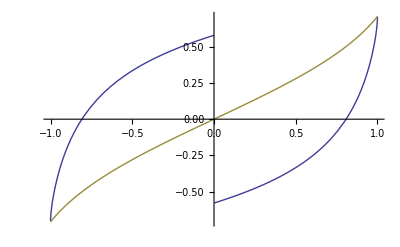

```mathematica
Plot[{kai1sim[f,Pi/4],kai2sim[f,Pi/4],kai3sim[f,Pi/4]},{f,-1,1}]
```

```mathematica
Plot[{kai2sim[f,Pi/2]},{f,-1,1}]
```

-Graphics-